## Computing Ramification Hits

## Joel’s system

p is the target polynomial.  g is the simple starting polynomial.  I chose one of the complex roots.

```mathematica
Clear[p,g,Dp,z1,z2]
p[{z1_,z2_}]:={z2-2 z1^2+z2^2,2-2 z2-z1+ 2 z1^2}
g[{z1_,z2_}]:={1-z1^2,1-z2^2}
Dp[{z1_,z2_}]:={{-4 z1,1+2 z2},{-1+4 z1,-2}}
Dg[{z1_,z2_}]:=-{{2z1,0},{0,2z2}}
tTarget=1/2;
TableForm[
RamData=NSolve[{
(1-tTarget)p[{z1,z2}]+tTarget γ g[{z1,z2}]==0,
Det[(1-tTarget)Dp[{z1,z2}]+tTarget γ Dg[{z1,z2}]]==0
},{z1,z2,γ}]
]
```

z1→-6.92002 | z2→10.8681 | γ→0.70833
z1→1.29849 | z2→0.44672 | γ→-3.97311
z1→-1.19635 | z2→0.246327 | γ→-5.92576
z1→0.893204+2.27213 ⅈ | z2→2.32327-0.547706 ⅈ | γ→-2.91998-0.119582 ⅈ
z1→0.893204-2.27213 ⅈ | z2→2.32327+0.547706 ⅈ | γ→-2.91998+0.119582 ⅈ
z1→0.0579956-0.0417957 ⅈ | z2→-1.33936-1.02622 ⅈ | γ→0.594381-1.73813 ⅈ
z1→0.0579956+0.0417957 ⅈ | z2→-1.33936+1.02622 ⅈ | γ→0.594381+1.73813 ⅈ
z1→2.08649 | z2→2.74875 | γ→0.47637
z1→0.268488 | z2→1.05085 | γ→-2.1672
z1→0.128798+0.695397 ⅈ | z2→0.101491-0.0688511 ⅈ | γ→-0.735386+0.210881 ⅈ
z1→0.128798-0.695397 ⅈ | z2→0.101491+0.0688511 ⅈ | γ→-0.735386-0.210881 ⅈ
z1→0.294428 | z2→0.654831 | γ→-0.996656

Joel use the value for γ below.

```mathematica
SetPrecision[γ/.RamData⟦5⟧,16]
```

-2.919984600272383+0.11958169743604 ⅈ

It should really break if you plug in all the digits correctly.  It will probably still struggle if you only put it in approximately.

## Rabeya’s system

```mathematica
Clear[p,g,Dp,Dg,z1,z2,z3]
p[{z1_,z2_,z3_}]:={z1+z2+z3, z1 z2 + z2 z3 + z1 z3,z1 z2 z3 -1}
g[{z1_,z2_,z3_}]:={z1^3-1,z2^3-1,z3^3-1}
Dp[{z1_,z2_,z3_}]=D[ p[{z1,z2,z3}],{{z1,z2,z3}}]
Dg[{z1_,z2_,z3_}]=D[g[{z1,z2,z3}],{{z1,z2,z3}}]
```

{{1,1,1},{z2+z3,z1+z3,z1+z2},{z2 z3,z1 z3,z1 z2}}

{{3 z1^2,0,0},{0,3 z2^2,0},{0,0,3 z3^2}}

Rabeya’s system has 142 of ramification points!

142

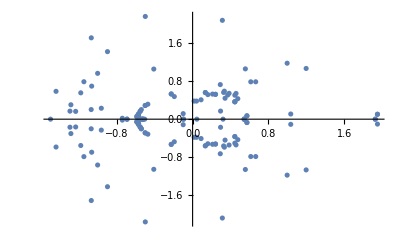

```mathematica
tTarget=1/2;
Eqs={
(1-tTarget)p[{z1,z2,z3}]+tTarget γ g[{z1,z2,z3}]==0,
Det[(1-tTarget)Dp[{z1,z2,z3}]+tTarget γ Dg[{z1,z2,z3}]]==0
};
RamData=NSolveValues[Eqs,{z1,z2,z3,γ}];
Length[RamData]
ListPlot[ ReIm[ RamData⟦All,4⟧]]
```

From the graph the nearest ones to γ=1 are approximately 1.04+ ± 0.11 ⅈ.

```mathematica
RamData=NSolveValues[
{
(1-tTarget)p[{z1,z2,z3}]+tTarget γ g[{z1,z2,z3}]==0,
Det[(1-tTarget)Dp[{z1,z2,z3}]+tTarget γ Dg[{z1,z2,z3}]]==0
},{z1,z2,z3, γ}];
RamData=Sort[RamData, (Abs[#1⟦4⟧-1]≤Abs[#2⟦4⟧-1])&];
NumberForm[RamData⟦1,4⟧,16]
TableForm[RamData⟦1;;10⟧,TableHeadings->{Automatic,{"z1","z2","z3","γ"}}]
```

1.035174734522851+0.1089704294441743 ⅈ

| z1 | z2 | z3 | γ
1 | 0.511647+0.73322 ⅈ | 0.174027-0.801092 ⅈ | 1.08487+0.064135 ⅈ | 1.03517+0.10897 ⅈ
2 | 0.511647-0.73322 ⅈ | 0.174027+0.801092 ⅈ | 1.08487-0.064135 ⅈ | 1.03517-0.10897 ⅈ
3 | -0.5-0.866025 ⅈ | 1.-1.65978×10^-8 ⅈ | -0.5+0.866025 ⅈ | 0.573012-0.0706475 ⅈ
4 | -0.5+0.866025 ⅈ | 1.+1.73936×10^-8 ⅈ | -0.5-0.866025 ⅈ | 0.573012+0.0706475 ⅈ
5 | -0.5-0.866025 ⅈ | 1.+1.33645×10^-8 ⅈ | -0.5+0.866025 ⅈ | 0.573012-0.0706476 ⅈ
6 | -0.5+0.866025 ⅈ | 1.-1.71347×10^-8 ⅈ | -0.5-0.866025 ⅈ | 0.573012+0.0706476 ⅈ
7 | -0.203723+0.838118 ⅈ | 1.0324+0.315726 ⅈ | -0.517009-0.886687 ⅈ | 0.543666+0.0065939 ⅈ
8 | -0.203723-0.838118 ⅈ | 1.0324-0.315726 ⅈ | -0.517009+0.886687 ⅈ | 0.543666-0.0065939 ⅈ
9 | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ | 1.-1.88618×10^-8 ⅈ | 0.445471+0.367273 ⅈ
10 | -0.5-0.866025 ⅈ | -0.5+0.866025 ⅈ | 1.-1.83347×10^-8 ⅈ | 0.445471+0.367273 ⅈ